```mathematica
funcmap1=Import["C:\\projects\\ZGeometry\\ZGeometry\\output\\funcmap1.txt", "Table"];
```

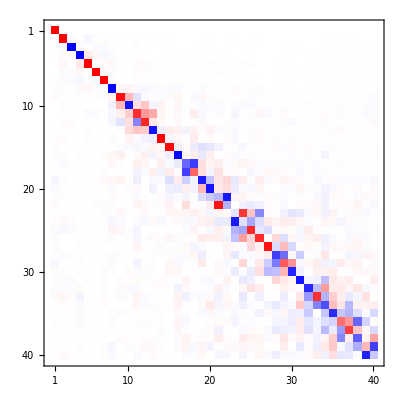

```mathematica
MatrixPlot[funcmap1,ColorFunctionScaling->False,ColorFunction->(If[#≤0,RGBColor[1+#,1+#,1],RGBColor[1,1-#,1-#]]&)]
```

```mathematica
funcmap2=Import["C:\\projects\\ZGeometry\\ZGeometry\\output\\funcmap2.txt", "Table"];
```

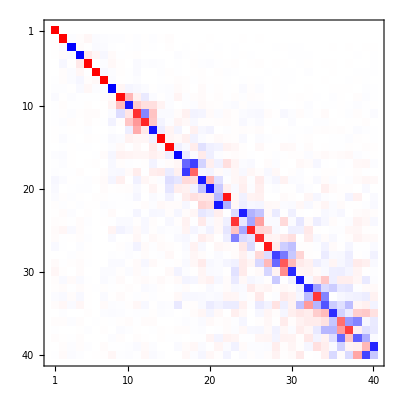

```mathematica
MatrixPlot[funcmap2,ColorFunctionScaling->False,ColorFunction->(If[#≤0,RGBColor[1+#,1+#,1],RGBColor[1,1-#,1-#]]&)]
```